# Pulsar Radiation of Freely-precessing NSs

## Section 3.1 Phase modulation and timing residuals

The rotation matrix from the body frame to the inertia frame

```mathematica
aa={{Cos[ϕ],Sin[ϕ],0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
bb={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
cc={{Cos[ψ],Sin[ψ],0},{-Sin[ψ],Cos[ψ],0},{0,0,1}};
R=Simplify[Inverse[cc.bb.aa]]
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ],Sin[θ] Sin[ϕ]},{Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Sin[θ] Sin[ψ],Cos[ψ] Sin[θ],Cos[θ]}}

The magnetic dipole moment in the body frame

```mathematica
m={Sin[χ],0,Cos[χ]}
```

{Sin[χ],0,Cos[χ]}

The magnetic dipole in the inertia frame

```mathematica
m1=R. m
```

{Cos[χ] Sin[θ] Sin[ϕ]+Sin[χ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]),-Cos[ϕ] Cos[χ] Sin[θ]+Sin[χ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]),Cos[θ] Cos[χ]+Sin[θ] Sin[χ] Sin[ψ]}

```mathematica
mx=m1[[1,;;]]
my=m1[[2,;;]]
```

Cos[χ] Sin[θ] Sin[ϕ]+Sin[χ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ])

-Cos[ϕ] Cos[χ] Sin[θ]+Sin[χ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])

```mathematica
tanΦ=my/mx
```

(-Cos[ϕ] Cos[χ] Sin[θ]+Sin[χ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]))/(Cos[χ] Sin[θ] Sin[ϕ]+Sin[χ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]))

Finally, we obtain the phase 
-Graphics-

For triaxial NS

```mathematica
Φ=ϕ[t]-π/2+ArcTan[(Cos[ψ[t]]Sin[χ])/(Sin[θ[t]]Cos[χ]-Sin[ψ[t]]Sin[χ]Cos[θ[t]])]
```

-π/2+ArcTan[(Cos[ψ[t]] Sin[χ])/(Cos[χ] Sin[θ[t]]-Cos[θ[t]] Sin[χ] Sin[ψ[t]])]+ϕ[t]

The residuals of period and period derivative are related to the phase residual as

When θ_min> χ, the precession-induced phase residual is

```mathematica
ΔΦ=ArcTan[(Cos[ψ[t]]Sin[χ])/(Sin[θ[t]]Cos[χ]-Sin[ψ[t]]Sin[χ]Cos[θ[t]])]
```

ArcTan[(Cos[ψ[t]] Sin[χ])/(Cos[χ] Sin[θ[t]]-Cos[θ[t]] Sin[χ] Sin[ψ[t]])]

```mathematica
DPhidot=Simplify[D[ΔΦ, t]]
```

(Sin[χ] (-Cos[ψ[t]] (Cos[χ] Cos[θ[t]]+Sin[χ] Sin[θ[t]] Sin[ψ[t]]) θ'[t]+(Cos[θ[t]] Sin[χ]-Cos[χ] Sin[θ[t]] Sin[ψ[t]]) ψ'[t]))/(Cos[ψ[t]]^2 Sin[χ]^2+(Cos[χ] Sin[θ[t]]-Cos[θ[t]] Sin[χ] Sin[ψ[t]])^2)

Calculate the time evolution of the Euler angles

```mathematica
n=3;
δ1=0.1;
I1=(1-1.3*10^-7)*10^45;
I3=10^45;
I2=(I3*δ1+I1)/(1+δ1);
ω0=100*2*π;
a=ω0*Sin[60/180*π];
w20=0;
b=ω0*Cos[60/180*π];
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
dt=301.7;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,k2]/I/K/2];
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]];
T1=2π/Re[(J/I1+2*I*π/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])];
time=Table[t,{t,0,n*T,dt}];
cosθ=Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
sinθ=Sin[ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]]];
cosψ=Cos[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
sinψ=Sin[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
```

```mathematica
T1
T
```

0.01

176054.

Plot cosθ and cosψ

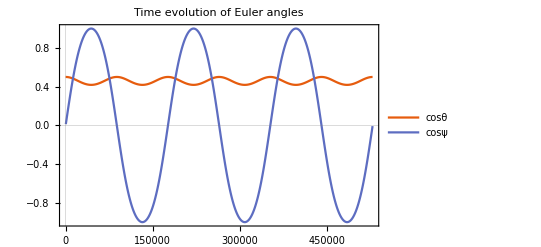

```mathematica
second=Transpose@{time,cosθ};
third=Transpose@{time,cosψ};
ListPlot[{second,third},Joined->True, PlotLegends->{"cosθ","cosψ"},PlotLabel->"Time evolution of Euler angles",PlotTheme->"Scientific",Axes->{True,False}]
```

The range of θ

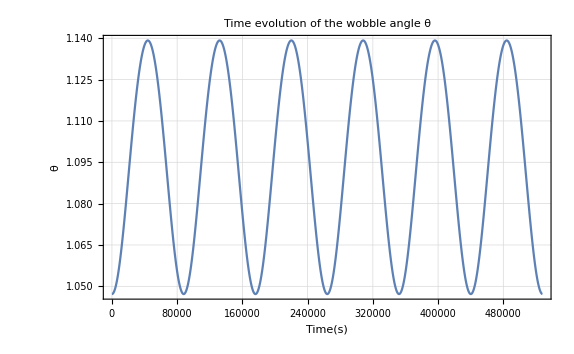

```mathematica
θ=ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]];
theta=Transpose@{time,θ};
ListPlot[theta,Joined->True,PlotTheme->"Detailed",PlotLabel->"Time evolution of the wobble angle θ",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[θ],None},{HoldForm[Time[s]],None}}]
```

```mathematica
θmax=Max[θ]
θmin=Min[θ]
```

1.13919

1.0472

The phase residual

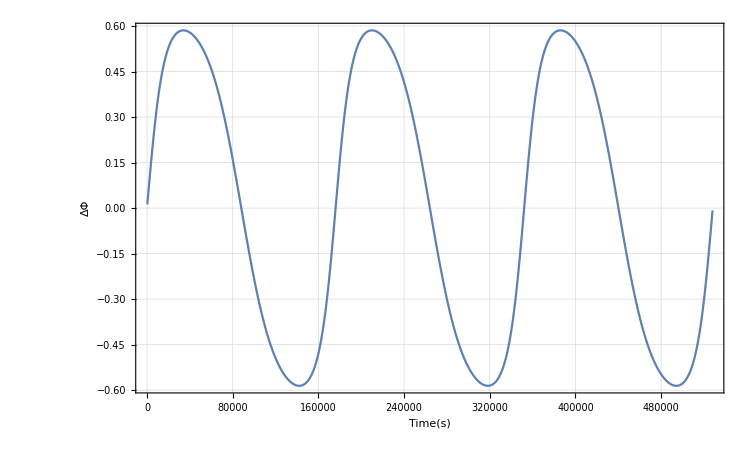

```mathematica
χ=30./180*π;
sinχ=Sin[χ];
cosχ=Cos[χ];
ΔΦ=ArcTan[(cosψ sinχ)/(cosχ sinθ-cosθ sinχ sinψ)];
PR=Transpose@{time,ΔΦ};
ListPlot[PR,Joined->True,PlotTheme->"Detailed",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[ΔΦ],None},{HoldForm[Time[s]],None}},GridLines->Automatic]
```

The time derivative of θ and ψ

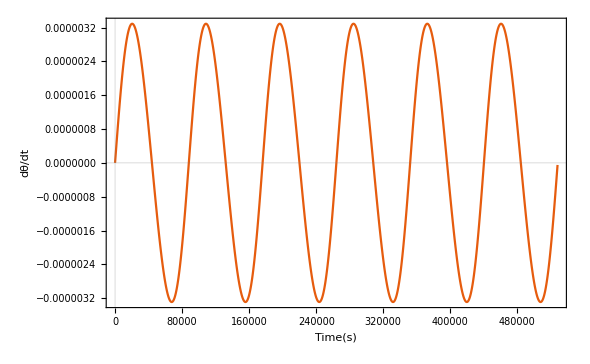

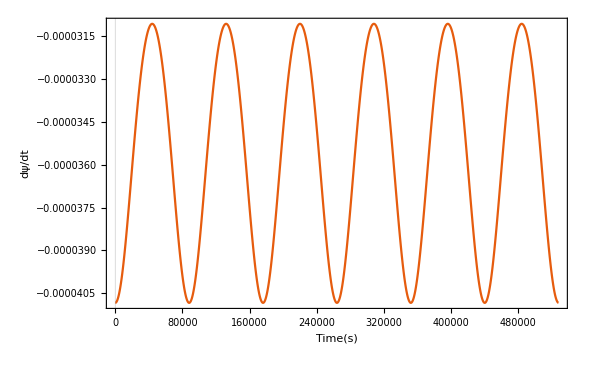

```mathematica
δ=1-1.0*√((I1(I3-I2))/(I2(I3-I1)));
dθ=Table[-1/J b I3 k2 taut JacobiCN[t taut,k2] JacobiSN[t taut,k2],{t,0,n*T,dt}]/(-sinθ);
dψ=Table[(taut*(-1+δ) JacobiDN[t*taut,k2])/((-1+δ)^2 JacobiCN[t*taut,k2]^2+JacobiSN[t*taut,k2]^2),{t,0,n*T,dt}];
dtheta=Transpose@{time,dθ};
ListPlot[dtheta,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[dθ/dt],None},{HoldForm[Time[s]],None}}]
dpsi=Transpose@{time,dψ};
ListPlot[dpsi,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[dψ/dt],None},{HoldForm[Time[s]],None}}]
```

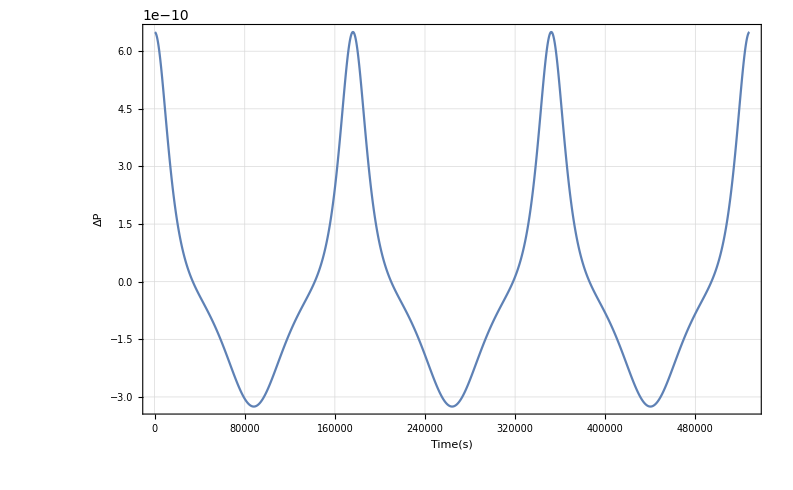

```mathematica
χ=30./180*π;
sinχ=Sin[χ];
cosχ=Cos[χ];

ΔP=((-cosψ sinχ (cosχ cosθ+sinχ sinθ sinψ) dθ+sinχ(cosθ sinχ-cosχ sinθ sinψ) dψ)/(cosψ^2 (sinχ)^2+(cosχ sinθ-cosθ sinχ sinψ)^2))*T1^2/2.0/π;
residual=Transpose@{time,ΔP};
ListPlot[residual,Joined->True,PlotTheme->"Detailed",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[ΔP],None},{HoldForm[Time[s]],None}}]
```

## Section 3.2 Pulse-width modulation

The polar angle Θ

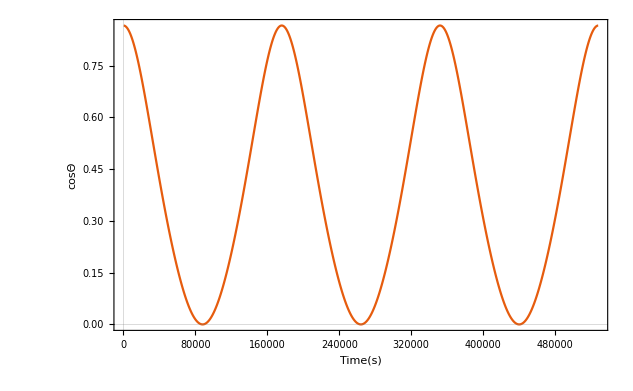

```mathematica
cosΘ=sinθ*sinψ*sinχ+ cosθ*cosχ;
CTheta=Transpose@{time,cosΘ};
ListPlot[{CTheta},Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[cosΘ],None},{HoldForm[Time[s]],None}}]
```

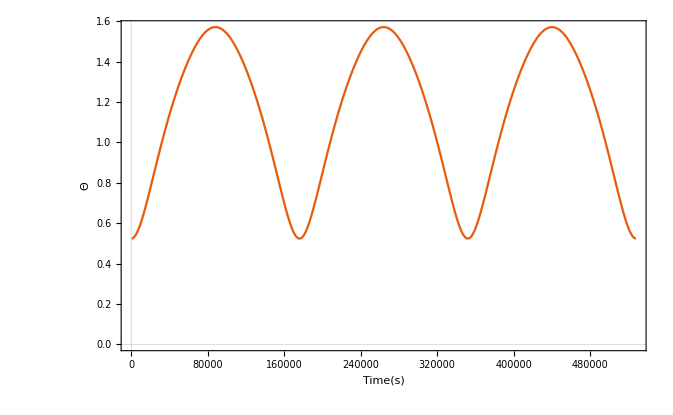

```mathematica
Θ=ArcCos[sinθ*sinψ*sinχ+ cosθ*cosχ];
Theta=Transpose@{time,Θ};
ListPlot[Theta,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[Θ ],None},{HoldForm[Time [s]],None}}]
```

The Pulse width

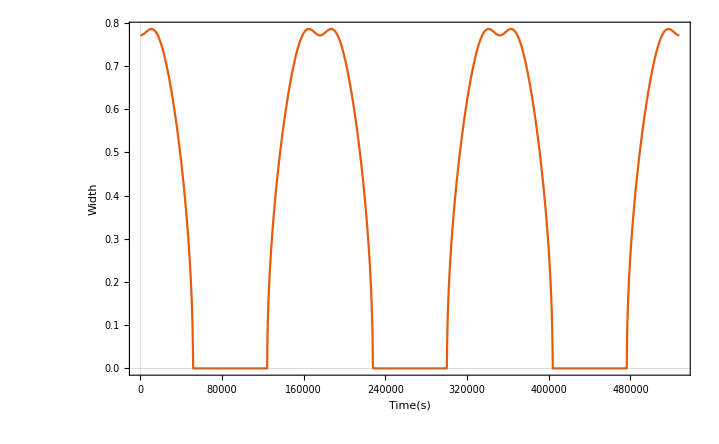

```mathematica
ι=45/180*π;(*inclination angle 的补角*)
ρ=30/180*π;
W=Re[ArcCos[(Cos[ρ]-Cos[Θ]Cos[ι])/(Sin[Θ]Sin[ι])]];
Width=Transpose@{time,W};
ListPlot[Width,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[Width ],None},{HoldForm[Time [s]],None}}]
Export["desktop/Precession/Radio_Waves/width_large.dat",Width];
```

When θ_max < χ, the phase residual is

```mathematica
Clear["Global`*"]  (*Clear all variables*)
```

```mathematica
ΔΦ=ArcTan[(Cos[ψ[t]]Sin[χ])/(Sin[θ[t]]Cos[χ]-Sin[ψ[t]]Sin[χ]Cos[θ[t]])]-ψ[t]-π/2
```

-π/2+ArcTan[(Cos[ψ[t]] Sin[χ])/(Cos[χ] Sin[θ[t]]-Cos[θ[t]] Sin[χ] Sin[ψ[t]])]-ψ[t]

Note that Jones & Anderrson 2001 has a typo in the denominator, so we check it

Arctan(x) + Arctan((1/x))=π/2, so

Using

```mathematica
phasex=(-(Cos[χ] Sin[θ]-Cos[θ] Sin[χ] Sin[ψ])/(Cos[ψ] Sin[χ])-Tan[ψ])/(1-(Cos[χ] Sin[θ]-Cos[θ] Sin[χ] Sin[ψ])/(Cos[ψ] Sin[χ])Tan[ψ])
```

(-Csc[χ] Sec[ψ] (Cos[χ] Sin[θ]-Cos[θ] Sin[χ] Sin[ψ])-Tan[ψ])/(1-Csc[χ] Sec[ψ] (Cos[χ] Sin[θ]-Cos[θ] Sin[χ] Sin[ψ]) Tan[ψ])

The phase residual is

```mathematica
n=3;
δ1=0.1;
I1=(1-1.3*10^-7)*10^45;
I3=10^45;
I2=(I3*δ1+I1)/(1+δ1);
ω0=100*2*π;;
a=ω0*Sin[1/180*π];
w20=0;
b=ω0*Cos[1/180*π];
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
dt=233.173;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,k2]/I/K/2];
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]];
T1=2π/Re[(J/I1+2*I*π/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])];
time=Table[t,{t,0,n*T,dt}];
cosθ=Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
sinθ=Sin[ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]]];
cosψ=Cos[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
sinψ=Sin[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
```

Power::infy: 碰到无穷表达式 1/0..

```mathematica
T
```

80690.5

Plot cosθ  and cosψ

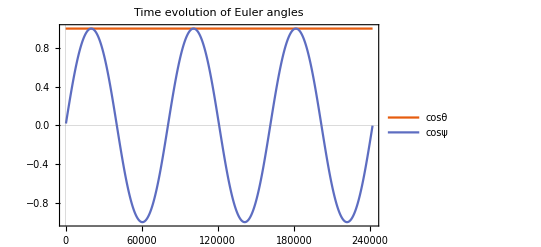

```mathematica
second=Transpose@{time,cosθ};
third=Transpose@{time,cosψ};
ListPlot[{second,third},Joined->True, PlotLegends->{"cosθ","cosψ"},PlotLabel->"Time evolution of Euler angles",PlotTheme->"Scientific",Axes->{True,False}]
```

Plot θ

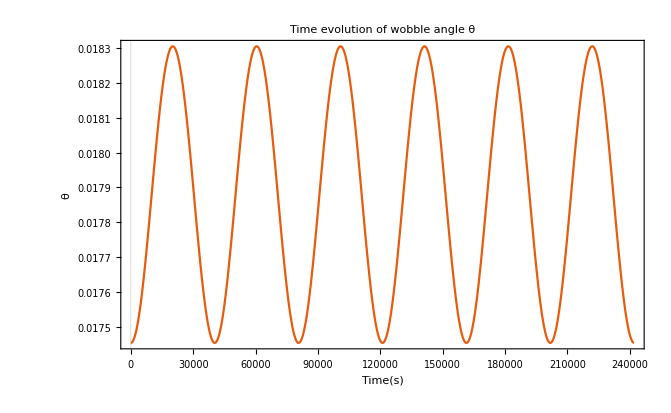

```mathematica
θ=ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]];
theta=Transpose@{time,θ};
ListPlot[theta,Joined->True,PlotTheme->"Scientific",PlotLabel->"Time evolution of wobble angle θ",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[θ],None},{HoldForm[Time[s]],None}}]
```

```mathematica
Max[θ]
Min[θ]
```

0.0183052

0.0174533

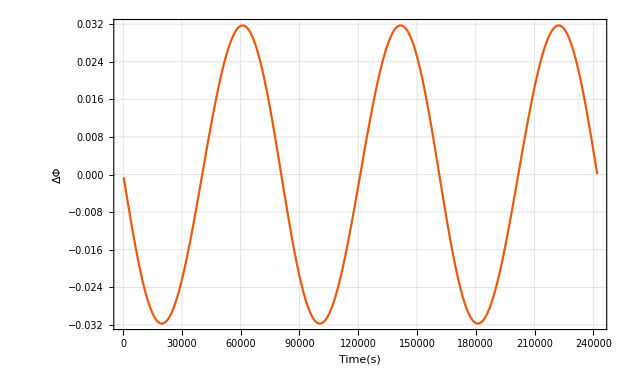

```mathematica
χ=30./180*π;
sinχ=Sin[χ];
cosχ=Cos[χ];
ΔΦ=ArcTan[(((cosθ-1)sinψ*sinχ-sinθ*cosχ)cosψ)/(cosψ*sinχ*cosψ+(cosθ*sinψ*sinχ-sinθ*cosχ)*sinψ)];
PR=Transpose@{time,ΔΦ};
ListPlot[PR,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[ΔΦ],None},{HoldForm[Time[s]],None}},GridLines->Automatic]
```

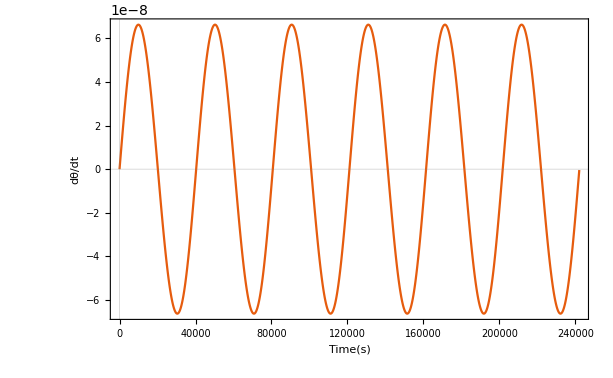

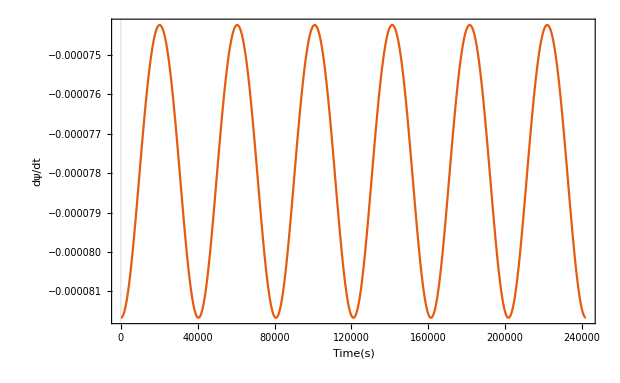

```mathematica
δ=1-1.0*√((I1(I3-I2))/(I2(I3-I1)));
dθ=Table[-1/J b I3 k2 taut JacobiCN[t taut,k2] JacobiSN[t taut,k2],{t,0,n*T,dt}]/(-sinθ);
dψ=Table[(taut*(-1+δ) JacobiDN[t*taut,k2])/((-1+δ)^2 JacobiCN[t*taut,k2]^2+JacobiSN[t*taut,k2]^2),{t,0,n*T,dt}];
dtheta=Transpose@{time,dθ};
ListPlot[dtheta,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[dθ/dt],None},{HoldForm[Time[s]],None}}]
dpsi=Transpose@{time,dψ};
ListPlot[dpsi,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[dψ/dt],None},{HoldForm[Time[s]],None}}]
```

Calculate the period residual

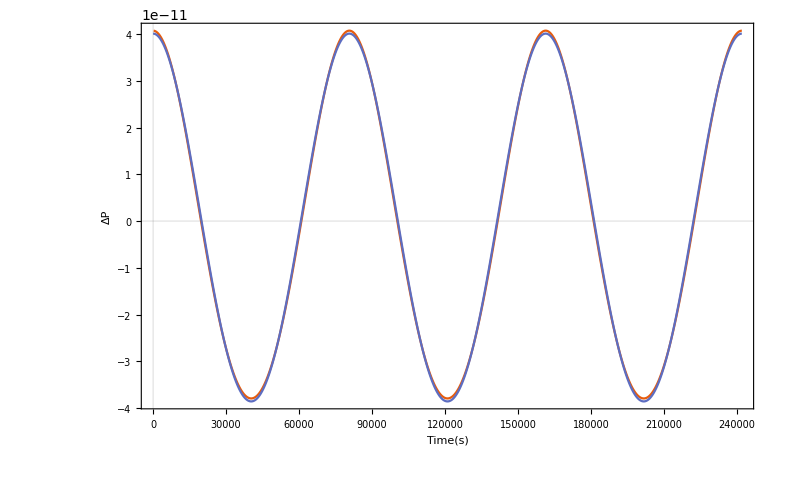

```mathematica
χ=30./180*π;
sinχ=Sin[χ];
cosχ=Cos[χ];
cotχ=Cot[χ];
ω2=2π/T;
δ1=0.1;
I1=(1-1.3*10^-7)*10^45;
I3=10^45;
I2=(I3*δ1+I1)/(1+δ1);
γ=I1*a/I3/b;
κ=1/16 I3/I1(I2-I1)/(I3-I2);
t=time;
term=T1^2/2.0/π*(cotχ  γ ω2  Cos[t ω2]+8 cotχ γ  κ  ω2  Cos[t ω2]+1/2(1+cotχ^2) γ^2 ω2 Cos[2*t*ω2]);
ΔP=-((-cosψ sinχ (cosχ cosθ+sinχ sinθ sinψ) dθ+sinχ(cosθ sinχ-cosχ sinθ sinψ) dψ)/(cosψ^2 (sinχ)^2+(cosχ sinθ-cosθ sinχ sinψ)^2)-dψ)*T1^2/2.0/π;
qq=-T1^2/2.0/π*dψ*sinθ*cosχ/sinχ*sinψ;
qq1=Transpose@{time,qq};
qq2=Transpose@{time,term};
residual=Transpose@{time,ΔP};
ListPlot[{residual,qq2},Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[ΔP],None},{HoldForm[Time[s]],None}}]
```

Pulse Width

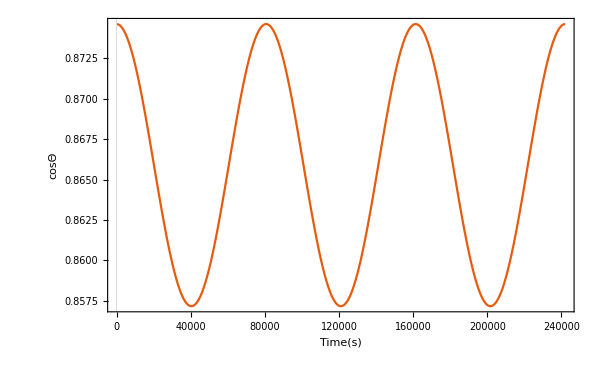

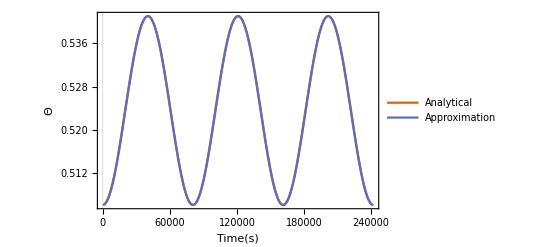

```mathematica
cosΘ=sinθ*sinψ*sinχ+ cosθ*cosχ;
CTheta=Transpose@{time,cosΘ};
ListPlot[CTheta,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[cosΘ],None},{HoldForm[Time[s]],None}}]
Θ=ArcCos[sinθ*sinψ*sinχ+ cosθ*cosχ];
Θ1=(χ-sinθ*sinψ);
Theta=Transpose@{time,Θ};
Theta1=Transpose@{time,Θ1};
ListPlot[{Theta,Theta1},Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[Θ ],None},{HoldForm[Time [s]],None}},PlotLegends->{"Analytical","Approximation"}]
```

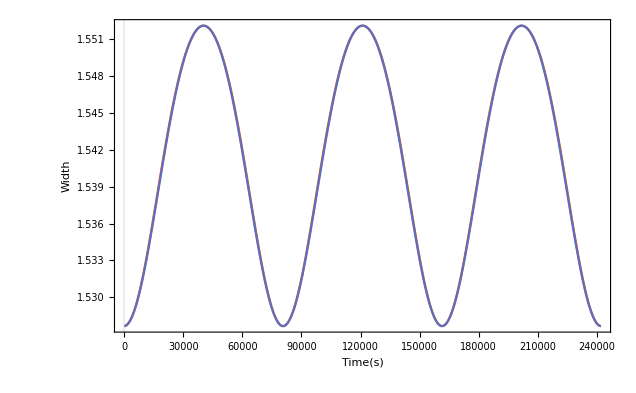

```mathematica
ι=45/180*π;
ρ=30/180*π;
W1=ArcCos[2((Cos[ρ]-Cos[Θ]Cos[ι])/(Sin[Θ]Sin[ι]))^2-1];
W2=ArcCos[2((Cos[ρ]-Cos[Θ1]Cos[ι])/(Sin[Θ1]Sin[ι]))^2-1];
Width1=Transpose@{time,W1};
Width2=Transpose@{time,W2};
Width=Transpose@{time,W1,W2};
ListPlot[{Width1,Width2},Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[Width ],None},{HoldForm[Time [s]],None}}]
```

### Small wobble angle approximation

```mathematica
Clear["Global`*"]  (*Clear all variables*)
```

```mathematica
cosϕ=Cos[t Subscript[Ω, 1]]
sinϕ=Sin[t Subscript[Ω, 1]]
cosθ=1-γ^2/2
sinθ=γ (1+8 κ Sin[t Subscript[Ω, 2]]^2)
cosψ=Sin[t Subscript[Ω, 2]]+(8 κ+32 κ^2) Cos[t Subscript[Ω, 2]]^2 Sin[t Subscript[Ω, 2]]+16 κ^2 Cos[t Subscript[Ω, 2]]^2 (1+3 Cos[2 t Subscript[Ω, 2]]) Sin[t Subscript[Ω, 2]]
sinψ=Cos[t Subscript[Ω, 2]]-(8 κ+32 κ^2) Cos[t Subscript[Ω, 2]] Sin[t Subscript[Ω, 2]]^2-96 κ^2 Cos[t Subscript[Ω, 2]]^3 Sin[t Subscript[Ω, 2]]^2
```

Cos[t Ω_1]

Sin[t Ω_1]

1-γ^2/2

γ (1+8 κ Sin[t Ω_2]^2)

Sin[t Ω_2]+(8 κ+32 κ^2) Cos[t Ω_2]^2 Sin[t Ω_2]+16 κ^2 Cos[t Ω_2]^2 (1+3 Cos[2 t Ω_2]) Sin[t Ω_2]

Cos[t Ω_2]-(8 κ+32 κ^2) Cos[t Ω_2] Sin[t Ω_2]^2-96 κ^2 Cos[t Ω_2]^3 Sin[t Ω_2]^2

```mathematica
Normal[Series[(a*x)/(b+c*x),{x,0,2}]]
```

(a x)/b-(a c x^2)/b^2

```mathematica
x1=Expand[(cosθ-1)*sinψ*Sin[χ]-sinθ*Cos[χ]]/.{γ^2 κ-> 0, γ^2 κ^2-> 0}
```

-γ Cos[χ]-1/2 γ^2 Cos[t Ω_2] Sin[χ]-8 γ κ Cos[χ] Sin[t Ω_2]^2

```mathematica
Expand[x1^2]
```

γ^2 Cos[χ]^2+γ^3 Cos[χ] Cos[t Ω_2] Sin[χ]+1/4 γ^4 Cos[t Ω_2]^2 Sin[χ]^2+16 γ^2 κ Cos[χ]^2 Sin[t Ω_2]^2+8 γ^3 κ Cos[χ] Cos[t Ω_2] Sin[χ] Sin[t Ω_2]^2+64 γ^2 κ^2 Cos[χ]^2 Sin[t Ω_2]^4

```mathematica
x2=γ^2 Cos[χ]^2
```

γ^2 Cos[χ]^2

```mathematica
x=x1+x2
```

-γ Cos[χ]+γ^2 Cos[χ]^2-1/2 γ^2 Cos[t Ω_2] Sin[χ]-8 γ κ Cos[χ] Sin[t Ω_2]^2

```mathematica
a=cosψ
b=Sin[χ]
c=sinψ
```

Sin[t Ω_2]+(8 κ+32 κ^2) Cos[t Ω_2]^2 Sin[t Ω_2]+16 κ^2 Cos[t Ω_2]^2 (1+3 Cos[2 t Ω_2]) Sin[t Ω_2]

Sin[χ]

Cos[t Ω_2]-(8 κ+32 κ^2) Cos[t Ω_2] Sin[t Ω_2]^2-96 κ^2 Cos[t Ω_2]^3 Sin[t Ω_2]^2

```mathematica
Resi=Coefficient[Expand[(a x)/b-(a c x^2)/b^2]/.κ-> 0,γ]*γ +Coefficient[Expand[(a x)/b-(a c x^2)/b^2]/.γ-> 0,κ]*κ+Coefficient[Expand[(a x)/b-(a c x^2)/b^2],γ*κ]*γ*κ+
Coefficient[Expand[(a x)/b-(a c x^2)/b^2]/.γ-> 0,κ^2]*κ^2+
Coefficient[Expand[(a x)/b-(a c x^2)/b^2]/.κ-> 0,γ^2]*γ^2
```

-γ Cot[χ] Sin[t Ω_2]+γ^2 (-1/2 Cos[t Ω_2] Sin[t Ω_2]+Cos[χ] Cot[χ] Sin[t Ω_2]-Cos[t Ω_2] Cot[χ]^2 Sin[t Ω_2])+γ κ (-8 Cos[t Ω_2]^2 Cot[χ] Sin[t Ω_2]-8 Cot[χ] Sin[t Ω_2]^3)

整理一下可得

```mathematica
Coefficient[Expand[-sinθ*Cot[χ]*Cos[ψ]-1/2 sinθ^2(1+2 Cot[χ]^2)sinψ*cosψ]/.κ-> 0,γ^2]
```

-1/2 Cos[t Ω_2] Sin[t Ω_2]-Cos[t Ω_2] Cot[χ]^2 Sin[t Ω_2]

If κ=0 , we can retrieve the results of Link & Epstein 2001, Jones & Anderrson 2001

Pulse width

```mathematica
Expand[sinθ*sinψ*Sin[χ]+cosθ*Cos[χ]]/.{γ^2 κ-> 0, γ^2 κ^2-> 0,γ κ^2-> 0, γ κ^3-> 0}
```

Cos[χ]-1/2 γ^2 Cos[χ]+γ Cos[t Ω_2] Sin[χ]

So the polar angle Θ can be approximated as

The same results as the biaxial one in this order. Same as Link & Epstein 2001

## Section 5 order of magnitudes analyse

```mathematica
P0=0.01;
Subscript[Ω, 2]=10^-5;
P0^2/2/π*Subscript[Ω, 2]
P0^2/4/π*Subscript[Ω, 2]
```

1.59155×10^-10

7.95775×10^-11